# Комиссаров А.Е. лаб5

## Задание 1

-Graphics--Graphics-

```mathematica
Пробел выполняет роль знака умножения
```

```mathematica
3 5
```

15

```mathematica
Дополнительные пробелы не важны
```

```mathematica
3                5
```

15

```mathematica
2+   7
```

9

```mathematica
2/3
```

2/3

```mathematica
Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.
```

```mathematica
17^(1/2)
```

√17

```mathematica
3      /7
```

3/7

```mathematica
Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.
```

```mathematica
17.          ^(1/2)
```

4.12311

```mathematica
Для изменения стандартного порядка выполнения операций используются скобки
```

```mathematica
3                   (6 +  5 )
```

33

## Задание 2 -Graphics-

```mathematica
С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision
```

```mathematica
N[Sqrt[17],200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

```mathematica
Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.
```

```mathematica
N[e^(x *Sqrt[163]), 40]
```

e^(12.76714533480370466171095200978089234738 x)

```mathematica
Вычислить
```

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
Вычислить
```

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

```mathematica
Последовательно введите выражение
```

```mathematica
5>3
5<2
```

True

False

```mathematica
Справедливо ли неравенство
```

```mathematica
Pi^E>E^Pi
```

False

# Задание 3 -Graphics--Graphics-

```mathematica
Решить уравнения
```

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

```mathematica
Решить системы уравнений
```

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

```mathematica
Придумать свою
```

```mathematica
NSolve[{(5 x^2+y^2+46y)/(y^2-4y)==4, x^3 y+y^4+x^4== 28}, {x,y}]
```

{{x→-0.0469283-3.60646 ⅈ,y→3.24297-2.49724 ⅈ},{x→-0.0469283+3.60646 ⅈ,y→3.24297+2.49724 ⅈ},{x→-2.39966,y→-1.00129},{x→2.23419-4.52611 ⅈ,y→0.246379+4.36771 ⅈ},{x→2.23419+4.52611 ⅈ,y→0.246379-4.36771 ⅈ},{x→-0.242495-2.43791 ⅈ,y→1.47718-0.424665 ⅈ},{x→-0.242495+2.43791 ⅈ,y→1.47718+0.424665 ⅈ},{x→3.03624,y→-1.50431}}

## Задание 4 Вариант 6

```mathematica
FindRoot[x^2-ⅇ^-x-2 == Sin[2x], {x,-1,2}]
```

{x→1.52185}

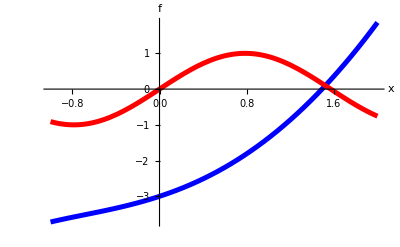

```mathematica
Plot[{x^2-ⅇ^-x-2, Sin[2x]}, {x, -1,2}, PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "f"}]
```

## Задание 5 вариант 6

```mathematica
sol1=NDSolve[{y''[x]+(1+  Cos[x])y [x]==0, y[0]==0, y'[0]==1},y, {x,0,5}]
```

{{y→InterpolatingFunction[…]}}

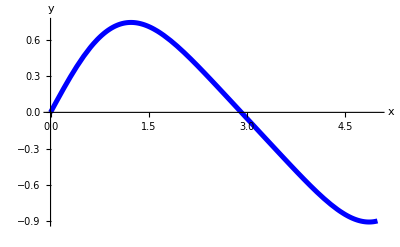

```mathematica
Plot[y[x]/.sol1, {x,0, 5}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
sol2=FindRoot[(y[x]/.sol1[[1]])==0, {x,2.9}]
```

{x→2.91805}

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2
```

-0.583582

```mathematica
FindMinimum[y[x]/.sol1[[1]], {x,5}]
```

{-0.908943,{x→4.87125}}

## ЗАДАНИЕ 6 вариант6

```mathematica
task2 = Table[{x,(5+4x+3Sin[x]+2Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,7.01815},{0.25,9.50912},{0.5,10.2122},{0.75,10.6966},{1.,11.8033},{1.25,13.1623},{1.5,13.0267},{1.75,15.6972},{2.,13.7951},{2.25,15.2713},{2.5,15.3886},{2.75,16.2916},{3.,15.3085},{3.25,14.9002},{3.5,17.3631},{3.75,15.4811},{4.,16.822},{4.25,16.7299},{4.5,21.308},{4.75,22.4709},{5.,23.6279}}

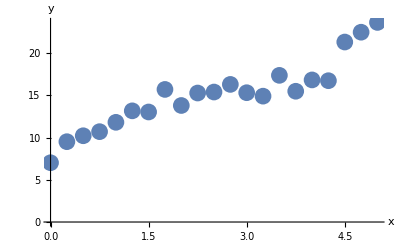

```mathematica
task2Plot=ListPlot[task2, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[task2, {1,x,Cos[x], Sin[x]},x]
```

4.45987+4.24101 x+2.38573 Cos[x]+3.01376 Sin[x]

5.85008+3.48848 x+1.44119 Cos[x]+2.42969 Sin[x]

```mathematica
y2=Fit[task2, {1,x,x^2, x^3, x^4},x]
```

7.4484+5.23955 x-0.0857397 x^2-0.54818 x^3+0.0983028 x^4

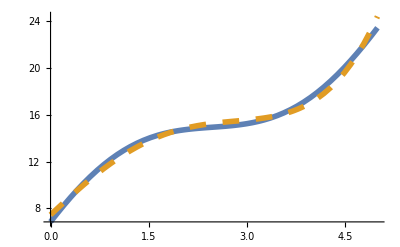

```mathematica
plot2 =Plot[{y1,y2}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

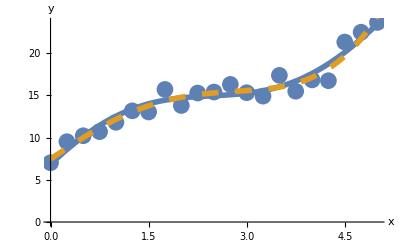

```mathematica
Show[task2Plot, plot2]
```